```mathematica
someMax={{1,0.1},{0.1,1}};
someMin={{-1,0},{0,-1}};
someSaddle={{1,0},{0,-1}};
charges={{2Pi{0.5,0.5},someMax},{2Pi{0.8,0.8},someMin},{2Pi{0.5,0.8},someSaddle},{2Pi{0.8,0.5},-someSaddle}};
```

```mathematica
normalizeDelta[delta_]:=If[delta<-Pi,2Pi-delta,If[delta>Pi,delta-2Pi,delta]]
chargeInfluence[charge_]=Function[{x,y},Module[{dx},
dx=normalizeDelta/@({x,y}-charge[[1]]);
((charge[[2]][[1]][[1]]+charge[[2]][[2]][[2]])/2-dx.charge[[2]].dx )Exp[-Norm[dx]^2]
]];
```

```mathematica
combined[coeffs_,charges_]=Function[{x,y},coeffs.(chargeInfluence[#][x,y]&)/@charges];
Clear[chargeLine]
chargeLine[q_]:=Graphics3D[{Thick,If[Det[q[[2]]]>0,Green,Red],InfiniteLine[Append[q[[1]],0],{0,0,1}]}];
(*Manipulate[
Show[{Plot3D[combined[{a,b,c,d},charges][x,y],{x,0,2Pi},{y,0,2Pi},ImageSize->Large,PlotRange->All],chargeLine/@charges}]
,{a,0,1},{b,0,1},{c,0,1},{d,0,1}]*)
```

```mathematica
Range[8]
```

{1,2,3,4,5,6,7,8}

```mathematica
(* This is where you get the noisyLaminarFlow from *)
recons=ArrayReshape[BinaryReadList["C:\\Users\\Sam\\Documents\\Wolfram Mathematica\\dynamics\\training_data\\recon"<>ToString[#-1]<>".dat","Real32"],{128,128}]&/@Range[8];
Mean[recons]//ListPlot3D
```

-Graphics3D-

```mathematica
BinaryWrite["C:\\Users\\Sam\\Documents\\Wolfram Mathematica\\dynamics\\noisyLaminarFlow.dat",Mean[recons]//Flatten,"Real32"]
```

```mathematica
ArrayReshape[BinaryReadList["C:\\Users\\Sam\\Documents\\Wolfram Mathematica\\dynamics\\noisyLaminarFlow.dat","Real32"],{128,128}]//ListPlot3D
```

-Graphics3D-

```mathematica
recon=ArrayReshape[BinaryReadList["C:\\Users\\Sam\\Documents\\Wolfram Mathematica\\dynamics\\training_data\\recon0.dat","Real32"],{128,128}];
orig=ArrayReshape[BinaryReadList["C:\\Users\\Sam\\Documents\\Wolfram Mathematica\\dynamics\\training_data\\reconOrig0.dat","Real32"],{128,128}];
```

```mathematica
laminar=ArrayReshape[BinaryReadList["C:\\Users\\Sam\\Documents\\Wolfram Mathematica\\dynamics\\laminarProfile.dat","Real32"],{128,128}];
ListPlot3D[laminar,PlotRange->All]
Fourier@laminar//ListPlot3D
```

-Graphics3D-

-Graphics3D-

```mathematica
Manipulate[ListPlot3D[Standardize/@{orig,recon, laminar}],{a,-1,1}]
```

Standardize::vectmat: The first argument is expected to be a vector or matrix.

General::stop: Further output of Standardize::vectmat will be suppressed during this calculation.

ListPlot3D::arrayerr: {Standardize[orig],Standardize[recon],Standardize[laminar]} must be a valid array or a list of valid arrays.

Standardize::vectmat: The first argument is expected to be a vector or matrix.

General::stop: Further output of Standardize::vectmat will be suppressed during this calculation.

ListPlot3D::arrayerr: {Standardize[orig],Standardize[recon],Standardize[laminar]} must be a valid array or a list of valid arrays.

```mathematica
domainSize=128;
fftDx=(2Pi/domainSize)Table[I x,{x,0,domainSize-1},{y,0,domainSize-1}];
fftDy=(2Pi/domainSize)Table[I y,{x,0,domainSize-1},{y,0,domainSize-1}];
fftD2=fftDx^2+fftDy^2;
fftID2=Map[If[#==0,0,1/#]&,fftD2,{2}];
(* Perform the operation f via multiplication in the Fourier domain *)
viaFFT[f_,ex_]:=(*Transpose@*)Re@InverseFourier[f Fourier[ex]];
curlDiscrete[ex_]:=viaFFT[fftDx,ex[[All,All,2]]]-viaFFT[fftDy,ex[[All,All,1]]]
uncurlDiscrete[ex_]:={viaFFT[fftDy,ex],viaFFT[-fftDx,ex]}
gradDiscrete[ex_]:={viaFFT[fftDx,ex],viaFFT[fftDy,ex]}
toVectorFieldRepr[ex_]:=Transpose[ex,{3,1,2}]
streamFuncDiscrete[ex_]:=viaFFT[-fftID2,curlDiscrete[ex]]
(*
discreteHess[ex_,pt_]:={{ListInterpolation[viaFFT[fftDx^2,ex]]@@pt,ListInterpolation[viaFFT[fftDx fftDy,ex]]@@pt},{ListInterpolation[viaFFT[fftDx fftDy,ex]]@@pt,ListInterpolation[viaFFT[fftDy^2,ex]]@@pt}}
*)
discreteHess[ex_,pt_]:={{Extract[viaFFT[fftDx^2,ex],pt],Extract[viaFFT[fftDx fftDy,ex],pt]},{Extract[viaFFT[fftDx fftDy,ex],pt],Extract[viaFFT[fftDy^2,ex],pt]}}
vortToVelocity[vort_]:=gradDiscrete[streamFuncDiscrete[vort]]
Clear[discreteToInterp,discreteToInterpNoMod,interpToDiscrete]
discreteToInterp[dis_]:=discreteToInterp[dis]=ListInterpolation[dis,{{0,2Pi},{0,2Pi}}][Mod[x,2Pi],Mod[y,2Pi]];
discreteToInterpNoMod[dis_]:=discreteToInterpNoMod[dis]=ListInterpolation[dis,{{0,2Pi},{0,2Pi}}];
interpToDiscrete[ifun_]:=interpToDiscrete[ifun]=Table[ifun[x(2Pi/domainSize),y(2Pi/domainSize)],{x,0,domainSize-1},{y,0,domainSize-1}];
skewDiscrete[l_]:=Map[{-#[[2]],#[[1]]}&,l,{2}];
discreteDiss[psi_]:=Total[(2Pi/domainSize)^(2)(fftDx Conjugate[fftDx] + fftDy Conjugate[fftDy])(Abs[viaFFT[fftDx,psi]]^2+Abs[viaFFT[fftDy,psi]]^2)//Flatten]
```

```mathematica
findMeanFlow[psis_]:=streamFuncDiscrete[toVectorFieldRepr[Mean[ParallelMap[gradDiscrete,psis]]]]
```

```mathematica
td10k=Import["C:\\Users\\Sam\\Documents\\Wolfram Mathematica\\dynamics\\trainingData10000.mat"];
%//TensorDimensions
```

TensorDimensions::rect: Nonrectangular array encountered.

{7}

```mathematica
td10k[[6]]//TensorDimensions
```

{10000,128,128}

```mathematica
meanFlow=findMeanFlow[td10k[[6]]];
%//TensorDimensions
BinaryWrite["C:\\Users\\Sam\\Documents\\Wolfram Mathematica\\dynamics\\meanFlow.dat",meanFlow//Flatten,"Real32"]
```

{128,128}

C:\Users\Sam\Documents\Wolfram Mathematica\dynamics\meanFlow.dat

```mathematica
ListPlot3D@meanFlow
```

-Graphics3D-

{{50,1},{50,1},{50,64,7},{1,1},{1,1},{50,128,128},{1,1}}

{50,128,128}

-Graphics3D-

{2,128,128}

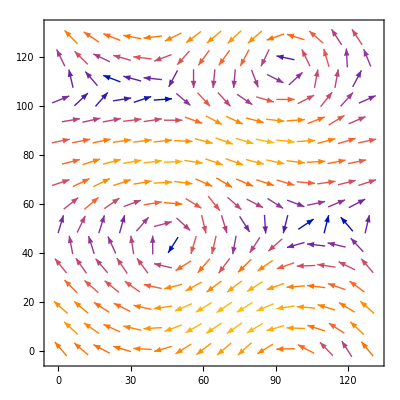

```mathematica
TensorDimensions/@td50
psiOuts=td50[[6]];
TensorDimensions@psiOuts
ListPlot3D[psiOuts[[30]]]
vField=gradDiscrete[psiOuts[[30]]];
%//TensorDimensions
ListVectorPlot[skewDiscrete@Transpose[vField,{3,1,2}]]
```

```mathematica
Export["td50anim.avi",ParallelTable[ListContourPlot[psi,PerformanceGoal->"Quality",ImageSize->Full,PlotLabel->"td50 stream function",PlotRange->{-3,3},Frame->None,PlotRangePadding->None],{psi,psiOuts}],AnimationRepetitions->∞,ImageResolution->200]
```

```mathematica
frames,AnimationRepetitions->∞]
```

```mathematica
Clear[frames]
```

```mathematica
Dynamic[MemoryInUse[]]
```